# Visualization of the approximate mixture model

## Interface to the library

```mathematica
convert[inp_?StringQ]:=ToExpression@StringReplace[inp,"e"->"*10^"];
Map[convert,ReadList["!/Users/philipp/Source/tfbayes/libphylotree/phylotree-approximation-test < /Users/philipp/Source/tfbayes/libphylotree/phylotree-parser-test2.nh",Record]];
```

## Visualization of the mixture model

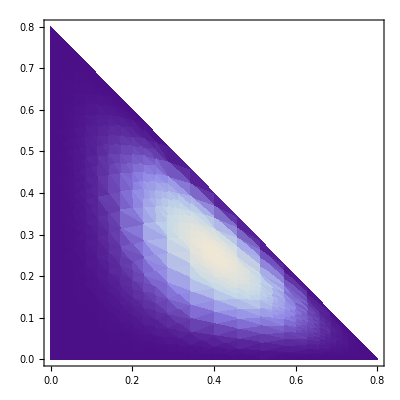

```mathematica
Pg=0.2;DensityPlot[100000000f[Pa,Pc,Pg,(1-Pa-Pc-Pg)],{Pa,0,1-Pg},{Pc,0,1-Pa-Pg}]
Remove[Pg];
```

## Visualization of the approximation

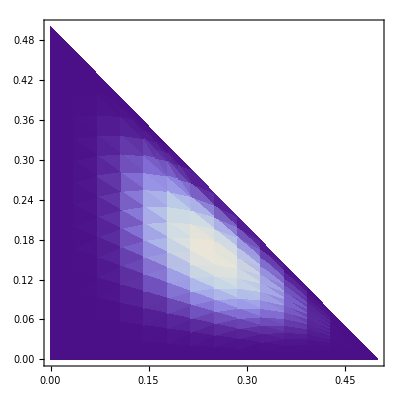

```mathematica
Pg=0.5;DensityPlot[g[Pa,Pc,Pg,(1-Pa-Pc-Pg)],{Pa,0,1-Pg},{Pc,0,1-Pa-Pg}]
Remove[Pg];
```

## Visual comparison of the four expectations

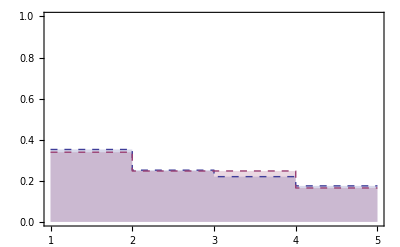

```mathematica
ListPlot[{Append[fxp,fxp[[4]]],Append[gxp,gxp[[4]]]},
InterpolationOrder->0,
PlotStyle->Dashed,
Joined->True,
Frame->True,
Filling->Axis,
PlotRange->{{1,5},{0,1}}]
```

## Simple example of the approximation

```mathematica
(* mixture weights *)
w={0.24433,0.3233,0.43237};
(* counts for each component *)
n1={3,4,5};
n2={2,7,4};
n3={4,4,5};
```

```mathematica
(* compute the first moment of the mixture model *)
w.Map[Moment[#,{1,0}]&,
{DirichletDistribution[n1],
DirichletDistribution[n2],
DirichletDistribution[n3]}]
```

0.243858

```mathematica
(* and the first moment of the approximation *)
Moment[DirichletDistribution[w.{n1,n2,n3}],{1,0}]
```

0.24374

## Numerical example with a two component mixture

```mathematica
α1=1;α2=1;
n1=14;n2=3;
m1=10;m2=4;
w={0.2,0.8};
Q[ξ1_,ξ2_,x_]:=((1-x)^(-1+ξ2) x^(-1+ξ1))/Beta[ξ1,ξ2]
P[x_]:=1/(w.{Beta[α1+n1,α2+n2],Beta[α1+m1,α2+m2]})w.{ (1-x)^(-1+n2+α2) x^(-1+n1+α1),(1-x)^(-1+m2+α2) x^(-1+m1+α1)}
H[ξ1_,ξ2_]:=Log[Beta[ξ1,ξ2]]+(ξ1+ξ2-2)PolyGamma[0,ξ1+ξ2]-(ξ1-1)PolyGamma[ξ1]-(ξ2-1)PolyGamma[ξ2]
NegKLDivergence[ξ1_,ξ2_]:=NIntegrate[Q[ξ1,ξ2,x]Log[P[x]],{x,0,1},WorkingPrecision->15]+H[ξ1,ξ2]
```

```mathematica
ContourPlot[
NegKLDivergence[x,y],{x,0.2,30},{y,0.2,10},
Contours->200,
ColorFunction->"DarkRainbow",
FrameLabel->{"ξ1","ξ2"},
Epilog->{Point[{α1+w.{ n1,m1},α2+w.{n2,m2}}],Line[{{0,0},{30,(α2+w.{n2,m2})/(α1+w.{n1,m1})30}}]}]
```

-Graphics-

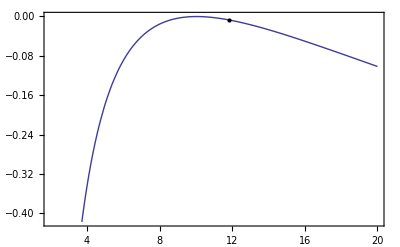

```mathematica
line[x_]:=NegKLDivergence[x,(α2+w.{n2,m2})/(α1+w.{n1,m1})x]
Plot[
line[x],{x,2,20},
Frame->True,
Epilog->Point[{α1+w.{ n1,m1},line[α1+w.{ n1,m1}]}]]
```

```mathematica
(* don't use x as variable, it causes some kind of name clash *)
NMaximize[{line[y],y>0},{y}]
```

{-0.000187922,{y→10.04}}

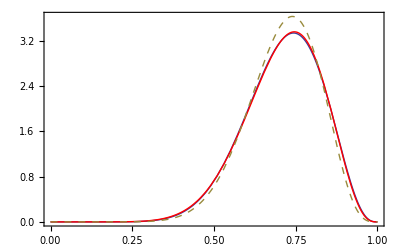

```mathematica
Plot[{P[x],Q[10.04,(α2+w.{n2,m2})/(α1+w.{n1,m1})10.04,x],Q[α1+w.{n1,m1},α2+w.{n2,m2},x]},{x,0,1},
Frame->True,
PlotStyle->{Thick,Red,Dashed}]
```

## Alternative approach

```mathematica
α1=1;α2=1;
n1=14;n2=3;
m1=10;m2=4;
w={0.2,0.8};
Q[ξ1_,ξ2_,x_]:=((1-x)^(-1+ξ2) x^(-1+ξ1))/Beta[ξ1,ξ2]
P[x_]:=1/(w.{Beta[α1+n1,α2+n2],Beta[α1+m1,α2+m2]})w.{ (1-x)^(-1+n2+α2) x^(-1+n1+α1),(1-x)^(-1+m2+α2) x^(-1+m1+α1)}
MSE[ξ1_,ξ2_]:=NIntegrate[(P[x]-Q[ξ1,ξ2,x])^2,{x,0,1}]
```

```mathematica
ContourPlot[
MSE[x,y],{x,0.2,30},{y,0.2,10},
Contours->100,
ColorFunction->"DarkRainbow",
FrameLabel->{"ξ1","ξ2"},
Epilog->Point[{α1+w.{ n1,m1},α2+w.{n2,m2}}]]
```

-Graphics-